```mathematica
SetDirectory[NotebookDirectory[]];
(files=FileNames["data/*.ods"])//TableForm
Needs["ErrorBarPlots`"]
Needs["ErrorBarPlots`"]
yagvsdiode=First@Import[files[[1]]];
yagvsdiode=erste[[1;;25]];
zweite=First@Import@files[[4]];
zweite=zweite[[1;;22]];
frequenz=First@Import@files[[2]];
frequenz=frequenz[[1;;24]];
pockels=First@Import@files[[3]];
pockels=pockels[[1;;21]];
PowerVsI={{200,41.9,0.1},{350,197,1},{500,359,2}};
```

data/erstemessung.ods
data/frequenzdoppel.ods
data/pockel.ods
data/zweitemesseung.ods

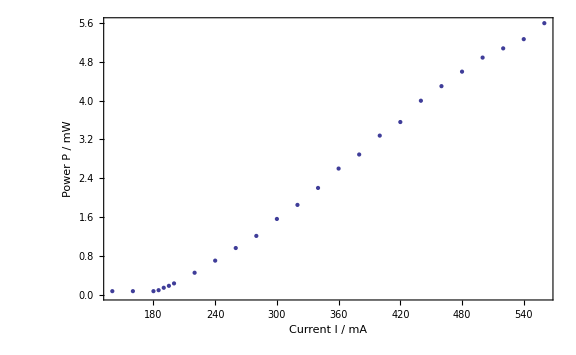

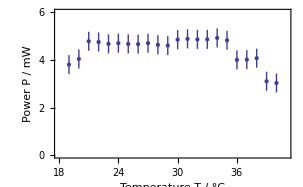

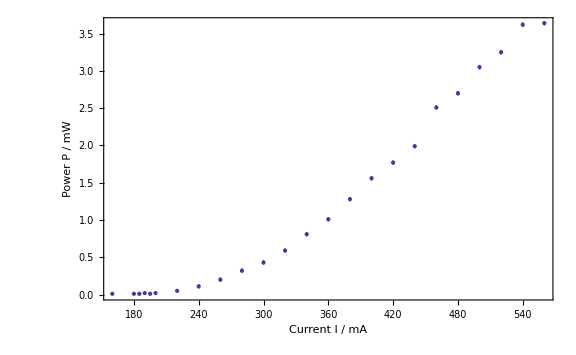

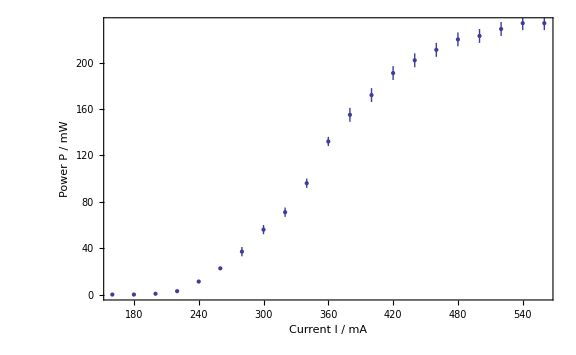

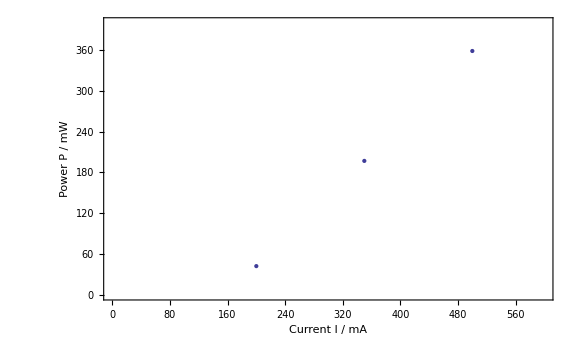

```mathematica
Show[ErrorListPlot[zweite,PlotRange->{{18,41},{0,6}}],ImageSize->Large,Frame->True,FrameLabel->{"Temperature T / °C","Power P / mW"},Axes->None]
Show[ErrorListPlot[frequenz],ImageSize->Large,Frame->True,FrameLabel->{"Current I / mA","Power P / mW"},Axes->None]
Show[ErrorListPlot[pockels],ImageSize->Large,Frame->True,FrameLabel->{"Current I / mA","Power P / mW"},Axes->None]
Show[ErrorListPlot[PowerVsI,PlotRange->{{0,600},{0,400}}],ImageSize->Large,Frame->True,FrameLabel->{"Current I / mA","Power P / mW"},Axes->None]
```

| Wert | Fehler
Steigung b | 1.04554 | 0.00474045
Achsenabschnitt a | -167.217 | 0.963763

Anzahl n: 3, R^2: 0.999878, χ^2/(n - 2): 5.94382

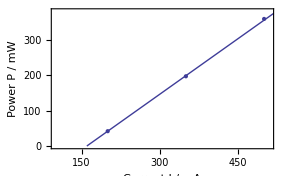

```mathematica
setz=LinReg[PowerVsI];
Show[Plot[(b*x+a/.setz),{x,0,520},PlotRange->{{100,510},{0,380}}],ErrorListPlot[PowerVsI],ImageSize->Large,Frame->True,FrameLabel->{"Current I / mA","Power P / mW"},Axes->None]
```

```mathematica
-167.21722846441946/1.0455430711610487
```

-159.933

```mathematica
b=1.045543071161048;
db=0.005;
da=0.96;
a=-159.933371543201;
```

```mathematica
YAG POWER VS DIODE POWER
```

```mathematica
Show[ErrorListPlot[yagvsdiode],ImageSize->Large,Frame->True,FrameLabel->{"Current I / mA","Power P / mW"},Axes->None]
```

```mathematica
yagvsdiode//TableForm
```

```mathematica
{{140, 0.07, 0.01}, {160, 0.07, 0.01}, {180, 0.07, 0.01}, {200, 0.23, 0.01}, {190, 0.14, 0.01}, {185, 0.09, 0.01}, {195, 0.18, 0.01}, {220, 0.45, 0.01}, {240, 0.7, 0.01}, {260, 0.96, 0.01}, {280, 1.21, 0.01}, {300, 1.56, 0.01}, {320, 1.85, 0.01}, {340, 2.2, 0.01}, {360, 2.6, 0.01}, {380, 2.89, 0.01}, {400, 3.28, 0.03}, {420, 3.56, 0.03}, {440, 4, 0.03}, {460, 4.3, 0.03}, {480, 4.6, 0.03}, {500, 4.89, 0.03}, {520, 5.08, 0.03}, {540, 5.27, 0.03}, {560, 5.6, 0.03}}
```

```mathematica
yagvsdiodcal=Table[{0,0,0,0},{i,Length[yagvsdiode]}];
```

```mathematica
For[i=1,i≤Length[yagvsdiodcal],i++,yagvsdiodcal[[i,1]]=((yagvsdiode[[i,1]]+a)*b);yagvsdiodcal[[i,2]]=-b*da+(yagvsdiode[[i,1]]-a)*db;yagvsdiodcal[[i,3]]=yagvsdiode[[i,2]];yagvsdiodcal[[i,4]]=yagvsdiode[[i,3]]]
```

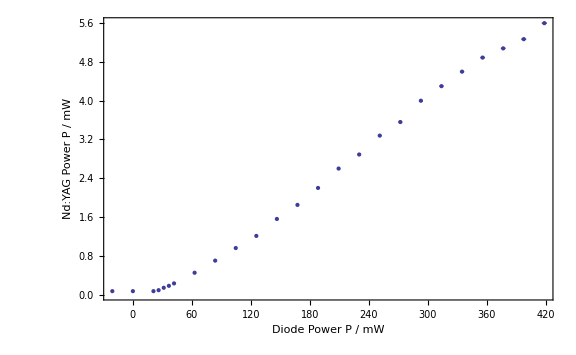

```mathematica
Show[ErrorListPlot[({{#[[1]],#[[3]]},ErrorBar[#[[2]],#[[4]]]}&/@yagvsdiodcal)],ImageSize->Large,Frame->True,FrameLabel->{"Diode Power P / mW","Nd:YAG Power P / mW"},Axes->None]
```

```mathematica
TEMPERATUR BLA
```

```mathematica
plateau temperatur 21 und 35 grad entsprechen bei 500mA
```

```mathematica
0.309*21+798.4
```

804.889

```mathematica
0.309*35+798.4
```

809.215